Тема 11. Невизначений та визначений інтеграл. Кратні інтеграли.

Завдання 1. Обчислення невизначеного інтеграла.

Використовуючи систему «Mathematica», обчислити невизначений інтеграл. Побудувати графіки підінтегрального виразу та первісної. На графіках інтервали зміни незалежної змінної підібрати самостійно.

```mathematica
f[x_]=(4*x-2)*Cos[2*x];
F[x_]=Integrate[f[x],x]
```

Cos[2 x]-Sin[2 x]+2 x Sin[2 x]

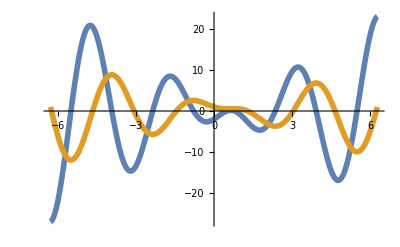

```mathematica
Plot[{f[x],F[x]},{x,-2π,2π},PlotStyle->Thickness[0.01]]
```

Завдання 2. Невизначений інтеграл різноманітних функцій.

Використовуючи систему «Mathematica», обчислити невизначений інтеграл. Побудувати графік підінтегрального виразу та його первісної. На графіках інтервали зміни незалежної змінної підібрати самостійно.

```mathematica
f[x_]=(x^2+Log[x^2])/x;
g[x_]=∫f[x]ⅆx
```

x^2/2+1/4 Log[x^2]^2

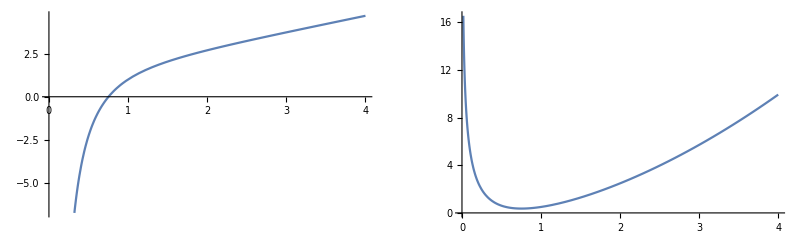

```mathematica
p1=Plot[f[x],{x,0,4}];
p2=Plot[g[x],{x,0,4}];
GraphicsRow[{p1,p2}]
```

Завдання 3. Невизначений інтеграл раціональних функцій.

Використовуючи систему «Mathematica», обчислити невизначений інтеграл. Побудувати графік підінтегрального виразу та його первісної, виключивши з них особливі точки. На графіках інтервали зміни незалежної змінної підібрати самостійно.

```mathematica
f[x_]=(x^3+6*x^2+14*x+10)/((x+1)*(x+2)^3);
q[x_]=Apart[f[x]]
```

1/(1+x)+2/(2+x)^3

```mathematica
F[x_]=∫q[x]ⅆx
```

-1/(2+x)^2+Log[1+x]

```mathematica
p1=Plot[f[x],{x,-10,10},PlotStyle->Thickness[0.015],Exclusions->{x==-1,x==-2}];
```

```mathematica
p2=Plot[F[x],{x,0,10},PlotStyle->Thickness[0.015]];
```

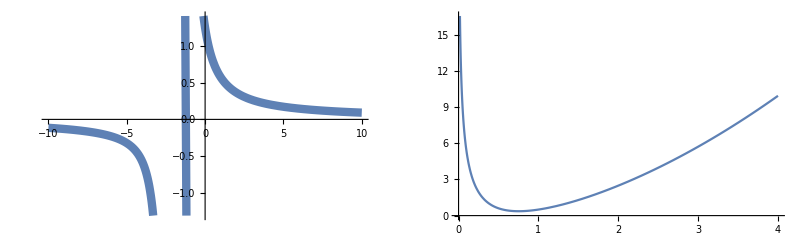

```mathematica
GraphicsRow[{p1,p2}]
```

Завдання 4. Обчислення визначеного інтеграла.

Використовуючи систему «Mathematica», обчислити визначений інтеграл. Побудувати графік підінтегрального виразу і зону, площу якої представляє інтеграл. При побудові кривої інтервал зміни незалежної змінної підбирати ширший за відрізок інтегрування.

```mathematica
f[x_]=(x+2)^2*Cos[x/2];
a=-1;b=1;
s=N[Integrate[f[x],{x,a,b}]]
```

8.28821

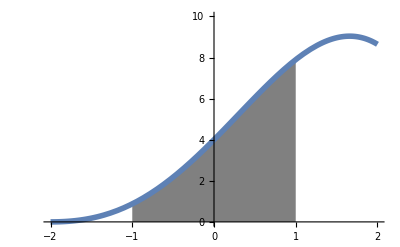

```mathematica
p1=Plot[f[x],{x,a,b},Filling->Axis,FillingStyle->Gray,PlotRange->{0,10}];
p2=Plot[f[x],{x,-2,2},PlotStyle->Thickness[0.01]];
Show[p1,p2,PlotRange->{{-2,2},{0,10}},AxesOrigin->{0,0}]
```

Завдання 5. Визначений інтеграл різноманітних функцій.

Використовуючи систему «Mathematica», обчислити визначений інтеграл. Побудувати графік підінтегрального виразу і область інтегрування. При побудові кривої інтервал зміни незалежної змінної підбирати ширший за відрізок інтегрування.

```mathematica
f[x_]=x^3/(x^2+4);
s=∫_0^2 f[x]ⅆx
```

2-Log[4]

```mathematica
s=N[s]
```

0.613706

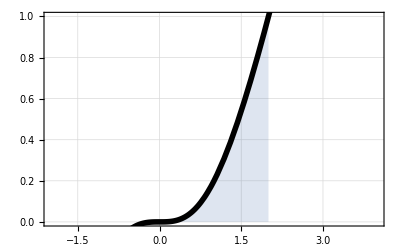

```mathematica
p1=Plot[f[x],{x,0,2},Filling->Axis,AxesOrigin->{0,0}];
p2=Plot[f[x],{x,-2,4},PlotStyle->{Thickness[0.01],Black}];
Show[{p1,p2},PlotRange->{{-2,4},{0,1}},Frame->True,GridLines->Automatic]
```

Завдання 6. Визначений інтеграл від тригонометричних виразів.

Використовуючи систему «Mathematica», обчислити визначений інтеграл. Побудувати графік підінтегрального виразу і область, площу якої представляє інтеграл. При побудові кривої інтервал зміни незалежної змінної підбирати ширший за відрізок інтегрування.

```mathematica
f[x_]=Sin[x/4]^2*Cos[x/4]^6;
s=∫_0^(2*π) f[x]ⅆx
```

(5 π)/64

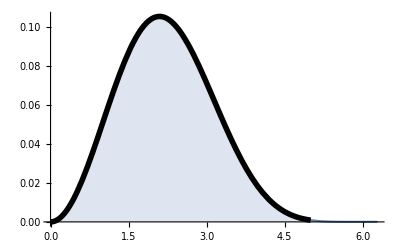

```mathematica
p1=Plot[f[x],{x,0,2*π},Filling->Axis,AxesOrigin->{0,0}];
p2=Plot[f[x],{x,0,5},PlotStyle->{Thickness[0.01],Black}];
Show[{p1,p2},PlotRange->All]
```

Завдання 7. Подвійний інтеграл як повторний.

Використовуючи систему «Mathematica», обчислити подвійний інтеграл по області D як повторний. Графічно зобразити область інтегрування D.

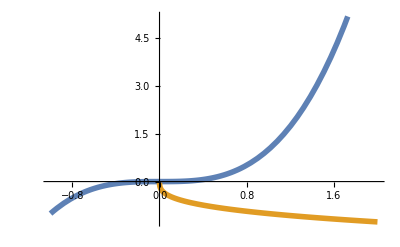

```mathematica
y1[x_]=x^3;
y2[x_]=-x^(1/3);
p1=Plot[{y1[x],y2[x]},{x,-1,2},PlotStyle->Thickness[0.01]]
```

```mathematica
Solve[y1[x]==y2[x],x,Reals]
```

{{x→0}}

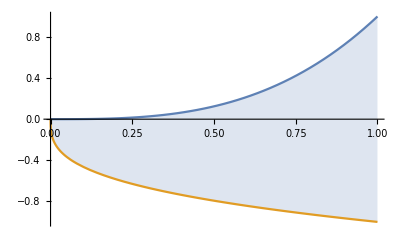

```mathematica
p2=Plot[{y1[x],y2[x]},{x,0,1},Filling->{1->{2}}]
```

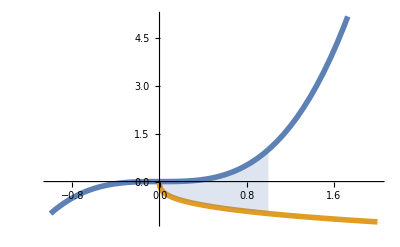

```mathematica
Show[p1,p2]
```

```mathematica
f[x_,y_]=18*x^2*y^2+32*x^3*y^3;
Integrate[f[x,y],{x,0,1},{y,-x^(1/3),x^3}]
```

1

Завдання 8. Обчислення подвійного інтеграла.

З’ясуйте до якого із зазначених вище типів відноситься ваша задача і, враховуючи його, обчисліть подвійний інтеграл по області D як повторний. Графічно зобразіть область D.

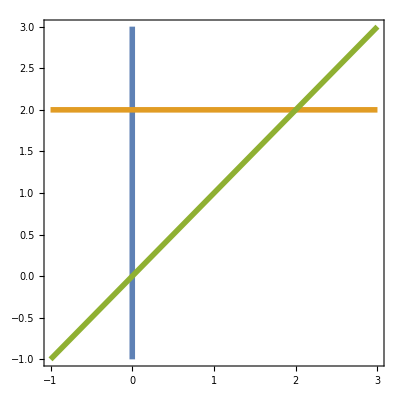

```mathematica
p1=ContourPlot[{x-0==0,y-2==0,y-x==0},{x,-1,3},{y,-1,3},ContourStyle->Thickness[0.01]]
```

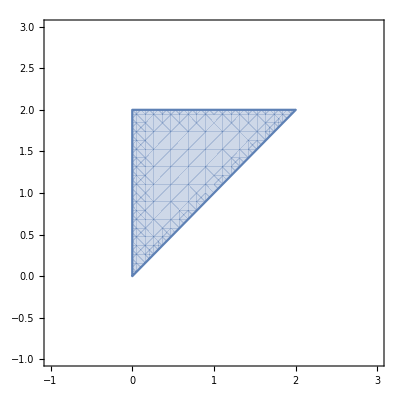

```mathematica
p2=RegionPlot[x<=y<=2&&0<=x<=2,{x,-1,3},{y,-1,3}]
```

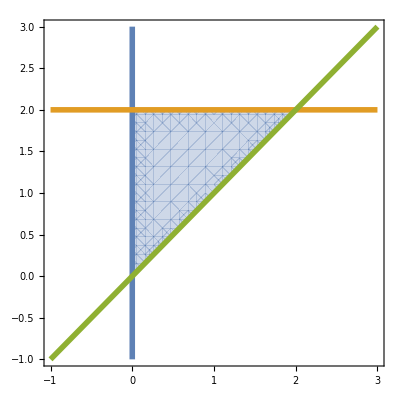

```mathematica
Show[p2,p1]
```

```mathematica
f[x_,y_]=y^2*Exp[-x*y/4];
F=N[Chop[∫_0^2 ∫_x^2 f[x,y]ⅆyⅆx]]
```

2.94304